## .08.08

## Dodelson 8.6

### Exercise 6. Obtain a semianalytic solution for Θ_0+Ψ and Θ_1 at recombination by carrying out the integrals Eq.8.24 and .8.26.

#### Initialization

```mathematica
<<Dodelson`ChangeVariable`
<<Dodelson`Definitions`
<<Dodelson`TESTCommonParameters`
SoundSubs;
EnergyDenSubs;
equalitySubs;
ayetaSubs
RecombinationSubs;
detadyx[y1_]:=detady/.y->y1
```

H::shdw: Symbol TraditionalForm`"H" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

c::shdw: Symbol TraditionalForm`"c" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Global`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

T::shdw: Symbol TraditionalForm`"T" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

k::shdw: Symbol TraditionalForm`"k" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

a::shdw: Symbol TraditionalForm`"a" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

x::shdw: Symbol TraditionalForm`"x" appears in multiple contexts TraditionalForm`{"CommonParameters`", "Definitions`"}; definitions in context TraditionalForm`"CommonParameters`" may shadow or be shadowed by other definitions.

defR ::  R(a_):=(3 ρ_m(a))/(4 ρ_γ(a))

defReta :: R_η(η_):=R(a)/.a→y(η) a_eq/.subC

Eqn819 ::  c_s(a_):=√(1/(3 (R(a)+1)))

Eqn819eta ::  c_s(eta_):=√(1/(3 (R_η(eta)+1)))

Eqn822 ::  r_s(η$_):=∫_0^η$ c_s(eta$170)ⅆeta$170

defRhoGR ::  ρ_γ(a_):=(C_γ (1/a)^4 ρ_cr)/h^2

defRhoM ::  ρ_m(a_):=(Ω_m ρ_cr)/a^3

defRhoCR ::  ρ_cr:=(3 H_0^2)/(8 π G)

Some definitions referencing 'equality' point :

defkeq :: k_eq→H(a_eq) a_eq

subkeq :: k_eq→√2 √((H_0^2 Ω_m)/a_eq)

subH0 :: H_0→(√((a_eq k_eq^2)/Ω_m))/(√2)

subkkeq :: k→k_eq kk_eq

subetat :: η'(t)→1/(a(η))

subyeta :: y(η)→(a(η))/a_eq

subDyeta :: y'(η)→(a'(η))/a_eq

subHt :: H→(a'(t))/(a(t))

defaeta :: a(η_):=y(η) a_eq

subHeta :: H→(a'(η))/(a(η))^2

defRhoGR ::  ρ_γ(a_):=(C_γ (1/a)^4 ρ_cr)/h^2

defRhoM ::  ρ_m(a_):=(Ω_m ρ_cr)/a^3

defRhoCR ::  ρ_cr:=(3 H_0^2)/(8 π G)

subaeq :: a_eq→C_γ/(h^2 Ω_m)

subC :: C_γ→h^2 a_eq Ω_m

η[a] = (2 √2 (√(h^2 (a+a_eq) Ω_m)-h √a_eq √Ω_m))/(h √a_eq k_eq √Ω_m)

η_y[y = a/a_eq] = (2 √2 (√(y+1)-1))/k_eq

Jacobian dη/dy => (√2)/(√(y+1) k_eq)
Or  -> dη/dy = (√a_eq)/(√(y+1) H_0 √Ω_m)

y[η] = 1/8 η k_eq (η k_eq+4 √2)

subZrecomb :: z_*→1000

subarecomb :: a_*→1/(z_*+1)

subyrecomb :: y_*→(a_*)/a_eq

#### Equation 8.24 definitions

```mathematica
Clear[Φ,Ψ]
Eqn824:=Module[{},holdint824=HoldForm[
integrand824[η_,eta_,kkeq_]:=(kkeq Subscript[k, eq])/(√3)(Φ[kkeq,eta]-Ψ[kkeq,eta]) Sin[Subscript[k, eq] kkeq( Subscript[r, s][η]-Subscript[r, s][eta])]
];
holdint824rs=HoldForm[
integrand824rs[rs_,rs1_,kkeq_]:=(kkeq Subscript[k, eq])/(√3)(Φ[kkeq,eta[rs1]]-Ψ[kkeq,eta[rs1]]) Sin[Subscript[k, eq] kkeq( rs-rs1)]
];
holdint824y=HoldForm[
integrand824y[y0_,y1_,kkeq_]:=(kkeq Subscript[k, eq])/(√3)(Φy[kkeq,y1]-Ψy[kkeq,y1]) Sin[Subscript[k, eq] kkeq( Subscript[r, s][Subscript[η, y][y0]]-Subscript[r, s][Subscript[η, y][y1]])]
];
hold824=HoldForm[
Subscript[Θ, 0][η]+Φ[η] == (Subscript[Θ, 0][0]+Φ[0])Cos[Subscript[k, eq] kkeq  Subscript[r, s][η]] + ∫_0^η integrand824[η,eta,kkeq]ⅆeta
];
hold824y=HoldForm[
Subscript[Θ, 0][Subscript[η, y][y]]+Φ[Subscript[η, y][y]] == (Subscript[Θ, 0][0]+Φ[0])Cos[Subscript[k, eq] kkeq  Subscript[r, s][Subscript[η, y][y]]] + ∫_0^y integrand824y[y,y1,kkeq] detadyx[y1] ⅆy1
];

hold824rs=HoldForm[
Subscript[Θ, 0][eta[rs]]+Φ[eta[rs]] == (Subscript[Θ, 00]+Subscript[Φ, 00])Cos[Subscript[k, eq] kkeq  rs] + ∫_0^rs integrand824rs[rs,rs1,kkeq]detadrs ⅆrs1
];

];
Eqn824;
(ReleaseHold[#]&)/@{hold824,holdint824,hold824y,holdint824y,defReta,defR,Eqn819eta,Eqn822};
cseta=Subscript[c, s][eta]//FullSimplify;
rstmp=Integrate[cseta,{eta,0,eta1},Assumptions->Element[eta1,Reals]&&Element[Subscript[k, eq],Reals]&&eta1>0&&Subscript[k, eq]>0
];
Subscript[r, s][η_]:=rstmp/.eta1->η;
Print["With : ",Eqn822," => ",Subscript[r, s][η]];
etaP[rs_]:=eta1/.Solve[rstmp==rs,eta1]
detadrs=D[etaP[rs1],rs1];
Clear[eta,h];

integrand824[η,Subscript[η, 1],kkeq]//Simplify;
tmp=%//PowerExpand//FullSimplify;
(ReleaseHold[#]&)/@{holdint824rs};
holdint824rs;
Print["The integrand of Eqn.8.24 using rs as the equation parameter and rs1 as the integration variable : ",
integrand824rs[rs,rs1,kkeq] detadrs
]
```

With : r_s(η$_):=∫_0^η$ c_s(eta$170)ⅆeta$170 => (4 √2 (sinh^-1(1/2 √(3/2) η k_eq+√3)-sinh^-1(√3)))/(3 k_eq)

The integrand of Eqn.8.24 using rs as the equation parameter and rs1 as the integration variable : {1/2 kkeq cosh(1/8 (3 √2 rs1 k_eq+8 sinh^-1(√3))) sin(kkeq (rs-rs1) k_eq) k_eq (Φ(kkeq,eta(rs1))-Ψ(kkeq,eta(rs1)))}

#### Figure 8.6 parameter values: η_*, k, r_s[η]

```mathematica
h=.5;
Subscript[Ω, m]=.015/h^2;
subPhi=Φ0->1;
Print["k_eq => keq = ",
keq=Subscript[k, eq]/.subkeq//NumericalValues];
Print["η :: recombination value -> η_* = ",
tmp=Subscript[η, y][SubStar[y]]/.subyrecomb/.subarecomb/.subZrecomb/.subkeq;
SubStar[η]=tmp//NumericalValues];
Print["η :: present day value -> η_0 = ",
tmp=Subscript[η, y][1/Subscript[a, eq]]," = ",
tmp=tmp/.subkeq ," = ",
Subscript[η, 0]=tmp//NumericalValues ];
Print["r_s  :: recombination value -> rsstar = ",
rsstar=Subscript[r, s][SubStar[η]]/.subkeq//NumericalValues,"
r_s  :: present day value -> rs0 = ",
rs0=Subscript[r, s][Subscript[η, 0]]/.subkeq//NumericalValues
];
Print["r_s k_eq  :: recombination value -> rsstarkeq = ",
rsstarkeq=keq Subscript[r, s][SubStar[η]]/.subkeq//NumericalValues,"
r_s k_eq   :: present day value -> rs0keq = ",
rs0keq=keq Subscript[r, s][Subscript[η, 0]]/.subkeq//NumericalValues
];
Print["k η_0 (in Fig.8.6) ranges to : ",2000," => k ranges from 0 to kmax = ",
kmax=2000/Subscript[η, 0]/.subkeq//NumericalValues];
Print["k/k_eq = kkeq range : ",rangekkeq={0,2000/Subscript[η, 0]/keq}/.subkeq//NumericalValues];
Print["η_* k_eq => etastarkeq = ",etastarkeq=SubStar[η] keq
];
Print["Check units in Mpc : keq = ",keq/sec2Mpc//NumericalValues,"
r_s[η_0] = ",Subscript[r, s][η]sec2Mpc/.subkeq/.η->Subscript[η, 0]//NumericalValues,"
r_s[η_*] = ",Subscript[r, s][η]sec2Mpc/.subkeq/.η->SubStar[η]//NumericalValues,"
y[η_*] = ",y[SubStar[η]]," = ",ystar=y[SubStar[η]]/.subkeq//NumericalValues,"
y[η_0] = ",y[Subscript[η, 0]]," = ",ymax=y[Subscript[η, 0]]/.subkeq//NumericalValues
];
```

k_eq => keq = 1.3811×10^-17

η :: recombination value -> η_* = 5.47928×10^16

η :: present day value -> η_0 = (2 √2 (√(1+1/a_eq)-1))/k_eq = (8.16497 (√(1+1/a_eq)-1))/(√(H_0^2/a_eq)) = 4.84617×10^18

r_s  :: recombination value -> rsstar = 2.87836×10^16
r_s  :: present day value -> rs0 = 4.2747×10^17

r_s k_eq  :: recombination value -> rsstarkeq = 0.39753
r_s k_eq   :: present day value -> rs0keq = 5.90379

k η_0 (in Fig.8.6) ranges to : 2000 => k ranges from 0 to kmax = 4.12697×10^-16

k/k_eq = kkeq range : {0,29.8818}

η_* k_eq => etastarkeq = 0.756743

Check units in Mpc : keq = 0.00142051
r_s[η_0] = 4156.11
r_s[η_*] = 279.851
y[η_*] = k_eq (3.75281×10^32 k_eq+3.87444×10^16) = 0.606681
y[η_0] = k_eq (2.93567×10^36 k_eq+3.42676×10^18) = 607.287

#### Plot Cos[k r_s[η_*] ]to verify units. Cos[k rs[η_*]] > Cos[k rs[eta_*]] > Cos[k rsstar] {k,0,2000/η_0} ⇒ Cos[keta0/η_0 rsstar]{keta0,0,2000}. Investigate Sin arguement in Eqn.8.24

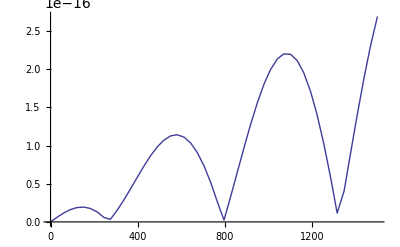

This plot varies from Fig.8.6 by : 
wavelength is longer by factor of 2.2<<look at rs,
the amplitude differs considerably <<look near k==0.

The arguement of the Sin[k r_s] term span 15.5037 to -214.744

What does the integrand824 look like? 
1/(√3)kkeq sin(4/3 √2 kkeq (sinh^-1(1/2 √(3/2) η k_eq+√3)-sinh^-1(1/2 √(3/2) k_eq η_1+√3))) k_eq (Φ(kkeq,η_1)-Ψ(kkeq,η_1))

What does the integrand824y look like? 
(kkeq sin(4/3 √2 kkeq (sinh^-1(√3 √(y0+1))-sinh^-1(√3 √(y1+1)))) k_eq (Φy(kkeq,y1)-Ψy(kkeq,y1)))/(√3)

0.606681

```mathematica
Plot[(keta0/Subscript[η, 0])Abs[Cos[(keta0/Subscript[η, 0]) rsstar ]],{keta0,0,1500}
]
Print["This plot varies from Fig.8.6 by : 
wavelength is longer by factor of 2.2<<look at rs,
the amplitude differs considerably <<look near k==0."];
(*look at arguement of Sin *) 
tmp=kkeq ( rsstarkeq - keq Subscript[r, s][eta])//NumericalValues;
krs0=tmp/.kkeq->39/.eta->Subscript[η, 0]/.subkeq//NumericalValues;
krs00=tmp/.kkeq->39/.eta->0/.subkeq//NumericalValues;
Print["The arguement of the Sin[k r_s] term span ",krs00," to ",krs0]; 
Print["What does the integrand824 look like? 
",
in824=integrand824[η,Subscript[η, 1],kkeq]//Simplify
];
Print["What does the integrand824y look like? 
",
in824y=integrand824y[y0,y1,kkeq]//Simplify
];
SubStar[y]/.subyrecomb/.subarecomb/.subZrecomb//NumericalValues
```

#### Definitions of functions 8.84--8.88

```mathematica
Φ[kkeq_,η_]:=Φy[kkeq,y[η]]
Ψ[kkeq_,η_]:=Ψy[kkeq,y[η]]
Φy[kkeq_,y_]:=Φbar[kkeq,y]((1-T[kkeq])ⅇ^(-.11(y kkeq)^1.6)+T[kkeq])
Ψy[kkeq_,y_]:=Ψbar[kkeq,y]((1-T[kkeq])ⅇ^(-.097( y kkeq)^1.6)+T[kkeq])
T[kkeq_]:=Log[1+.171 kkeq]/(.171 kkeq)(1+.284 kkeq+(1.18 kkeq  )^2+(.399 kkeq )^3+(.49 kkeq )^4)^(-.25)
Φbar[kkeq_,y_]:=3/4(1/kkeq )^2(y+1)/y^2 Subscript[Δ, T][y]
Ψbar[kkeq_,y_]:=-3/4(1/kkeq )^2(y+1)/y^2(Subscript[Δ, T][y]+.65 N2[y]/(1+y))
N2[y_]:=-0.1(20 y +19)/(3 y +4)y^2/(y+1)Φls[y]-8/3 y/(3 y +4)+8/9 Log[3 y/4+1]
Subscript[Δ, T][y_]:=(1.16-(.48 y)/(y+1))Φls[y] y^2/(y+1)
Φls0[y_]:=Φ0/10 1/y^3(16 √(1+y)+9 y^3+2 y^2-8 y-16)
PhiSeries[y_]:=(Series[Φls0[yyy],{yyy,0,3}]//Normal)/.yyy->y;
Φls[y_]:=If[y<.01,PhiSeries[y],Φls0[y]]
(*******************)
ni=10;
ymax0=10^-6 ymax;
Print["Truncation problem in Φls0[y] : ",
list=Table[{yx=i ymax0/ni,xser=PhiSeries[yx]/Φ0,xser-Φls0[yx]/Φ0},{i,1,ni}],"last column should be 0.
Using series approximation for small y : ",PhiSeries
];

ymax0=10^-0 ymax;
Print["Investigate Φy[kkeq,y]  : ",
list=Table[{yx=i ymax0/ni,xser=Φy[kkeq,yx]/Φ0/.kkeq->10^-5},{i,1,ni}],"
which show that Φy is sensitive as kkeq -> 0 "
];
Print["Investigate  Φy[kkeq,y1]-Ψy[kkeq,y1] : ",
list=Table[{yx=i ymax0/ni,xser=(  Φy[kkeq,yx]-Ψy[kkeq,yx])/Φ0/.kkeq->10^-05/.subPhi},{i,1,ni}],"
which show that Φy[kkeq,y1]-Ψy[kkeq,y] becomes sensitive as kkeq -> 0 "
];
Clear[k]
integrand824[η,eta,kkeq]/.Subscript[k, eq]->keq/.kkeq->1/.eta->1/keq/.η->2/keq/.Φ0->1
```

Truncation problem in Φls0[y] : (0.0000607287 | 0.999996 | 0.00223196
0.000121457 | 0.999992 | -0.00015124
0.000182186 | 0.999989 | -8.15765×10^-6
0.000242915 | 0.999985 | -0.0000349016
0.000303644 | 0.999981 | -3.99601×10^-6
0.000364372 | 0.999977 | 2.4916×10^-6
0.000425101 | 0.999973 | 3.2158×10^-6
0.00048583 | 0.99997 | 2.59311×10^-6
0.000546559 | 0.999966 | -2.63191×10^-6
0.000607287 | 0.999962 | 8.32414×10^-7)last column should be 0.
Using series approximation for small y : PhiSeries

Investigate Φy[kkeq,y]  : (60.7287 | 4.65861×10^9
121.457 | 4.62467×10^9
182.186 | 4.6132×10^9
242.915 | 4.60743×10^9
303.644 | 4.60396×10^9
364.372 | 4.60164×10^9
425.101 | 4.59999×10^9
485.83 | 4.59874×10^9
546.559 | 4.59777×10^9
607.287 | 4.597×10^9)
which show that Φy is sensitive as kkeq -> 0

Investigate  Φy[kkeq,y1]-Ψy[kkeq,y1] : (60.7287 | 9.27333×10^9
121.457 | 9.22653×10^9
182.186 | 9.21096×10^9
242.915 | 9.20319×10^9
303.644 | 9.19854×10^9
364.372 | 9.19544×10^9
425.101 | 9.19323×10^9
485.83 | 9.19157×10^9
546.559 | 9.19028×10^9
607.287 | 9.18925×10^9)
which show that Φy[kkeq,y1]-Ψy[kkeq,y] becomes sensitive as kkeq -> 0

3.99606×10^-18

#### Investigate integrand 8.24

```mathematica
keq
ni=10;
in0=in824/.Subscript[η, 1]->eta1/.η->SubStar[η]/.Subscript[k, eq]->keq/.subPhi//NumericalValues;

in1=in0/.kkeq->1;
in2[xkkeq_]:=in0/.kkeq->xkkeq
in2[10^-25]/keq/.eta1->SubStar[η] 10^-5 ;

Table[{yx=i ymax0/ni,xser=in2[kkeq]/.kkeq->10^-10/.subPhi/.eta1->Subscript[η, 0]},{i,1,ni}];

Print["More direct evaluation"]
Clear[yx,kkeq,ni,s]
ymax0
ni=20;
Table[{yx=i ymax0/ni,sub={kkeq->10^-05,subPhi,y1->yx};
tmp=Sin[Subscript[k, eq] kkeq( Subscript[r, s][Subscript[η, y][ymax]]-Subscript[r, s][Subscript[η, y][y1]])](  Φy[kkeq,y1]-Ψy[kkeq,y1]  )/.sub//Simplify;
tmp/.subPhi//NumericalValues  },
{i,1,ni}]
in2[kkeq];
in824;
```

1.3811×10^-17

More direct evaluation

607.287

(30.3644 | 261392.
60.7287 | 199819.
91.0931 | 164365.
121.457 | 139338.
151.822 | 119971.
182.186 | 104167.
212.551 | 90815.9
242.915 | 79256.
273.279 | 69062.8
303.644 | 59946.8
334.008 | 51701.8
364.372 | 44175.5
394.737 | 37252.6
425.101 | 30843.5
455.466 | 24876.9
485.83 | 19295.9
516.194 | 14053.4
546.559 | 9110.69
576.923 | 4435.39
607.287 | 0.)

#### Investigate integrand 8.24y

```mathematica
Print["Check accuracy of eta -> y transformation."]
in824y;
in824a=in824y//NumericalValues//Simplify;
in2y[xkkeq_]:=in824a/.kkeq->xkkeq
in2y[10^-5]/.y0->y[Subscript[η, 0]]/.y1->y[SubStar[η]]/.Subscript[k, eq]->keq//NumericalValues

Print["More direct evaluation"]
Clear[kkeq,ni]
ystar
ni=20;
Table[{yx=i ymax0/1000000000000000000000/ni,sub={kkeq->10^-20,subPhi,y1->yx,y0->ystar};
tmp=(kkeq Subscript[k, eq])/(√3)Sin[Subscript[k, eq] kkeq( Subscript[r, s][Subscript[η, y][y0]]-Subscript[r, s][Subscript[η, y][y1]])](  Φy[kkeq,y1]-Ψy[kkeq,y1])/.sub//Simplify;
tmp/.sub//NumericalValues  ,
tmp1=in824y/.sub//Simplify;
tmp1/.sub//NumericalValues,
tmp/tmp1},{i,1,ni}]
Print["Small values of y significant to integral."]
```

Check accuracy of eta -> y transformation.

1.00427×10^-12 (0.0000312328 Φ0+9.52703×10^-6 (2.55345 Φ0+0.336557))

More direct evaluation

0.606681

(3.03644×10^-20 | -33.9276 | -33.9276 | 1.
6.07287×10^-20 | -16.9638 | -16.9638 | 1.
9.10931×10^-20 | -11.3092 | -11.3092 | 1.
1.21457×10^-19 | -8.48191 | -8.48191 | 1.
1.51822×10^-19 | -6.78552 | -6.78552 | 1.
1.82186×10^-19 | -5.6546 | -5.6546 | 1.
2.12551×10^-19 | -4.8468 | -4.8468 | 1.
2.42915×10^-19 | -4.24095 | -4.24095 | 1.
2.73279×10^-19 | -3.76974 | -3.76974 | 1.
3.03644×10^-19 | -3.39276 | -3.39276 | 1.
3.34008×10^-19 | -3.08433 | -3.08433 | 1.
3.64372×10^-19 | -2.8273 | -2.8273 | 1.
3.94737×10^-19 | -2.60982 | -2.60982 | 1.
4.25101×10^-19 | -2.4234 | -2.4234 | 1.
4.55466×10^-19 | -2.26184 | -2.26184 | 1.
4.8583×10^-19 | -2.12048 | -2.12048 | 1.
5.16194×10^-19 | -1.99574 | -1.99574 | 1.
5.46559×10^-19 | -1.88487 | -1.88487 | 1.
5.76923×10^-19 | -1.78566 | -1.78566 | 1.
6.07287×10^-19 | -1.69638 | -1.69638 | 1.)

Small values of y significant to integral.

#### Plot integrals [ k eta0 ] at recombination.

{kmax→3.09523×10^-16}

22.4113

6.07287×10^-38

1/(√(y1+1))5.57039×10^-26 (0.597291 (0.681566+0.318434 ⅇ^(-0.131975 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.597291 (0.681566+0.318434 ⅇ^(-0.116378 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(2.11296 (1.52778-sinh^-1(√3 √(y1+1))))
 -1.02293×10^11
=============

1/(√(y1+1))3.15109×10^-25 (0.149323 (0.466981+0.533019 ⅇ^(-0.400074 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.149323 (0.466981+0.533019 ⅇ^(-0.352793 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(4.22592 (1.52778-sinh^-1(√3 √(y1+1))))
 -2.61095×10^11
=============

1/(√(y1+1))8.68339×10^-25 (0.0663657 (0.345109+0.654891 ⅇ^(-0.765397 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.0663657 (0.345109+0.654891 ⅇ^(-0.674941 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(6.33888 (1.52778-sinh^-1(√3 √(y1+1))))
 -3.9996×10^11
=============

1/(√(y1+1))1.78253×10^-24 (0.0373307 (0.267582+0.732418 ⅇ^(-1.2128 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.0373307 (0.267582+0.732418 ⅇ^(-1.06947 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(8.45184 (1.52778-sinh^-1(√3 √(y1+1))))
 -4.64287×10^11
=============

1/(√(y1+1))3.11395×10^-24 (0.0238916 (0.214511+0.785489 ⅇ^(-1.73318 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.0238916 (0.214511+0.785489 ⅇ^(-1.52835 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(10.5648 (1.52778-sinh^-1(√3 √(y1+1))))
 -4.20517×10^11
=============

1/(√(y1+1))4.91206×10^-24 (0.0165914 (0.176365+0.823635 ⅇ^(-2.32025 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.0165914 (0.176365+0.823635 ⅇ^(-2.04604 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(12.6778 (1.52778-sinh^-1(√3 √(y1+1))))
 -2.62768×10^11
=============

1/(√(y1+1))7.22156×10^-24 (0.0121896 (0.147941+0.852059 ⅇ^(-2.96927 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.0121896 (0.147941+0.852059 ⅇ^(-2.61836 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(14.7907 (1.52778-sinh^-1(√3 √(y1+1))))
 -1.46853×10^10
=============

1/(√(y1+1))1.00835×10^-23 (0.00933267 (0.126149+0.873851 ⅇ^(-3.67652 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00933267 (0.126149+0.873851 ⅇ^(-3.24202 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(16.9037 (1.52778-sinh^-1(√3 √(y1+1))))
 2.75083×10^11
=============

1/(√(y1+1))1.35361×10^-23 (0.00737397 (0.109045+0.890955 ⅇ^(-4.43896 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00737397 (0.109045+0.890955 ⅇ^(-3.91435 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(19.0166 (1.52778-sinh^-1(√3 √(y1+1))))
 5.43246×10^11
=============

1/(√(y1+1))1.76151×10^-23 (0.00597291 (0.095353+0.904647 ⅇ^(-5.25403 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00597291 (0.095353+0.904647 ⅇ^(-4.6331 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(21.1296 (1.52778-sinh^-1(√3 √(y1+1))))
 7.25947×10^11
=============

1/(√(y1+1))2.23546×10^-23 (0.00493629 (0.0842067+0.915793 ⅇ^(-6.11957 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00493629 (0.0842067+0.915793 ⅇ^(-5.39635 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(23.2426 (1.52778-sinh^-1(√3 √(y1+1))))
 7.73578×10^11
=============

1/(√(y1+1))2.77868×10^-23 (0.00414786 (0.075+0.925 ⅇ^(-7.03368 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00414786 (0.075+0.925 ⅇ^(-6.20243 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(25.3555 (1.52778-sinh^-1(√3 √(y1+1))))
 6.6302×10^11
=============

1/(√(y1+1))3.39425×10^-23 (0.00353427 (0.0672985+0.932702 ⅇ^(-7.9947 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00353427 (0.0672985+0.932702 ⅇ^(-7.04987 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(27.4685 (1.52778-sinh^-1(√3 √(y1+1))))
 4.04531×10^11
=============

1/(√(y1+1))4.08513×10^-23 (0.0030474 (0.060784+0.939216 ⅇ^(-9.00114 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.0030474 (0.060784+0.939216 ⅇ^(-7.93737 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(29.5814 (1.52778-sinh^-1(√3 √(y1+1))))
 4.1525×10^10
=============

1/(√(y1+1))4.85416×10^-23 (0.00265463 (0.0552192+0.944781 ⅇ^(-10.0517 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00265463 (0.0552192+0.944781 ⅇ^(-8.86376 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(31.6944 (1.52778-sinh^-1(√3 √(y1+1))))
 -3.5696×10^11
=============

1/(√(y1+1))5.70408×10^-23 (0.00233317 (0.0504238+0.949576 ⅇ^(-11.1451 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00233317 (0.0504238+0.949576 ⅇ^(-9.82797 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(33.8074 (1.52778-sinh^-1(√3 √(y1+1))))
 -7.09771×10^11
=============

1/(√(y1+1))6.63756×10^-23 (0.00206675 (0.0462589+0.953741 ⅇ^(-12.2804 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00206675 (0.0462589+0.953741 ⅇ^(-10.829 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(35.9203 (1.52778-sinh^-1(√3 √(y1+1))))
 -9.40426×10^11
=============

1/(√(y1+1))7.65715×10^-23 (0.00184349 (0.0426158+0.957384 ⅇ^(-13.4564 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00184349 (0.0426158+0.957384 ⅇ^(-11.8661 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(38.0333 (1.52778-sinh^-1(√3 √(y1+1))))
 -9.93687×10^11
=============

1/(√(y1+1))8.76536×10^-23 (0.00165455 (0.0394089+0.960591 ⅇ^(-14.6723 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00165455 (0.0394089+0.960591 ⅇ^(-12.9383 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(40.1462 (1.52778-sinh^-1(√3 √(y1+1))))
 -8.48369×10^11
=============

1/(√(y1+1))9.96462×10^-23 (0.00149323 (0.0365694+0.963431 ⅇ^(-15.9273 y1^1.6)) (1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)]+1/y1^2 0.00149323 (0.0365694+0.963431 ⅇ^(-14.0449 y1^1.6)) (y1+1) (((1.16-(0.48 y1)/(y1+1)) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/(y1+1)+(0.65 (-(0.1 (20 y1+19) If[y1<0.01,PhiSeries(y1),Φls0(y1)] y1^2)/((y1+1) (3 y1+4))-(8 y1)/(3 (3 y1+4))+8/9 log((3 y1)/4+1)))/(y1+1))) sin(42.2592 (1.52778-sinh^-1(√3 √(y1+1))))
 -5.23498×10^11
=============

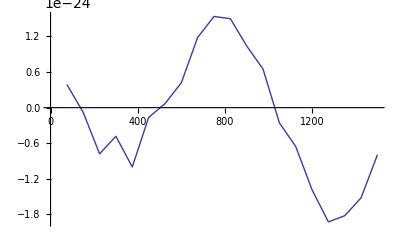

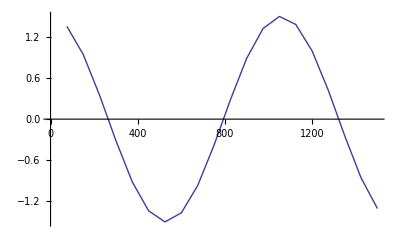

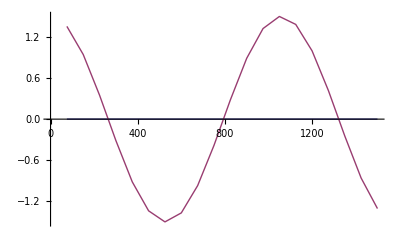

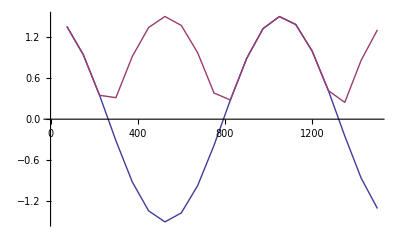

```mathematica
Clear[kmax]
keta0max=1500;
sub=Solve[kmax Subscript[η, 0]== keta0max,kmax][[1]]
kkeqmax=kmax/Subscript[k, eq]/.sub//NumericalValues
ymin=10^-40 ymax
ni=20;
Φ0=1;
subTheta0=Θ0->Φ0/2;

list=Table[{
xketa=i keta0max/ni,
xkkeq=xketa/(Subscript[η, 0] Subscript[k, eq]);
sub={kkeq->xkkeq,y0->ystar,subPhi};
integrand=(kkeq Subscript[k, eq])^(3/2) detadyx[y1]in824y/.sub/.subkeq//NumericalValues;
ylim1=y[xketa/(xkkeq Subscript[k, eq])]//NumericalValues;
List[integrand,"
 ",integrand/.y1->ymin,"
============="];
NIntegrate[integrand,{y1,ymin,ylim1},
Method->{"LocalAdaptive"}]
},{i,1,ni}];
ListLinePlot[Tooltip[list,"∫"],PlotRange->{{0,keta0max},Full},AxesLabel->{"kη_0"}]

list1=Table[{
xketa=i keta0max/ni,
xkkeq=xketa/(Subscript[η, 0] Subscript[k, eq]);sub={kkeq->xkkeq,y0->ystar}; (Φ0+Θ0) Cos[(xketa/Subscript[η, 0]) rsstar ]/.subTheta0/.sub
},{i,1,ni}];
ListLinePlot[Tooltip[list1,"Φ_0Cos"],PlotRange->{{0,keta0max},Full},AxesLabel->{"kη_0"}]
list2=Table[{list[[i,1]],list[[i,2]]+list1[[i,2]]},{i,1,Length[list]}];
list3=Table[{list[[i,1]],Abs[list[[i,2]]+list1[[i,2]]]},{i,1,Length[list]}];
ListLinePlot[{Tooltip[list,"∫"],Tooltip[list1,"Φ_0Cos"]},PlotRange->{{0,keta0max},Full},AxesLabel->{"kη_0"}]
ListLinePlot[{Tooltip[list2,"∫+Φ_0Cos"],Tooltip[list3,"|∫+Φ_0Cos|"]},PlotRange->{{0,keta0max},Full},AxesLabel->{"kη_0"}]
```

The premordial value of Φ[0] influences the relative contribution of the integral term verse the Cos term.  This is due to the N2 function which has a compoent that is not proportional to Φ[0].  Is this correct?  In the plots above we choose Φ[0] such that the influence of the Cos and integral terms are comparable.  There is still a difference between these plots and Fig.8.6 in the book. This may be due to the Cos and Sin arguements and it may be dependent upon the difference between the computation of r_s.

#### Investigate Hu-Sugiyama Fig.1 parameters. Conclusion: our k r_sis consistent.

```mathematica
Begin["Private`"];
Print["'a' limits for Fig.1 : ",alimits={10^-6,.001},"
=> y limits : ",
ylimits=alimits/Subscript[a, eq]//NumericalValues,"
k value (1/sec) for Fig.1 : ",
keval=.065sec2Mpc//NumericalValues,"
a at first 0 : ",
afirst0=6.8 10^-5,"
=> y at first 0 : ",
yfirst0=afirst0/Subscript[a, eq],"
=> eta0 : ",
eta0=Subscript[η, y][yfirst0],"
=> k r_s : ", 
keval Subscript[r, s][eta0]//NumericalValues,"
=> k r_s/π : ",
keval Subscript[r, s][eta0]/π//NumericalValues,"
which is close to the zero point of Cos.
This corresponds to keval η_0 : ",keval Subscript[η, 0],"
<=this value seem too large
",Subscript[η, 0]
]
End[];
```

'a' limits for Fig.1 : {1/1000000,0.001}
=> y limits : {0.000607287,0.607287}
k value (1/sec) for Fig.1 : 6.31968×10^-16
a at first 0 : 0.000068
=> y at first 0 : 0.000068/a_eq
=> eta0 : (2 √2 (√(1+0.000068/a_eq)-1))/k_eq
=> k r_s : 1.51565
=> k r_s/π : 0.482446
which is close to the zero point of Cos.
This corresponds to keval η_0 : 3062.62
<=this value seem too large
4.84617×10^18

#### Investigate the integration variables

```mathematica
Clear[integrand824Hu,krs,Φ,Ψ,k]
yke[kkeq_,keta_]:=y[keta/(kkeq Subscript[k, eq])]/.Subscript[k, eq]->k/kkeq//Simplify
Φ[kkeq_,kη_]:=Φy[kkeq,yke[kkeq,kη]]
Ψ[kkeq_,kη_]:=Ψy[kkeq,yke[kkeq,kη]]
Print[
"Since ",∫_0^η k fn[eta1]ⅆeta1,"=>",∫_0^ηk fn[keta1/k]ⅆketa1,"
The integrand of Eqn.8.24 : ",holdint824,"
The Sin[k r_s[eta]] => Sin[ keta/eta r_s[keta/k]] "]
Print["We define krs[kkeq,keta]:= k r_s[η] "]
Clear[krs,kkeq]
krs[kkeq0_,keta0_]:=Module[{kkeq,krs0,eta1,tmp,keta1},
Clear[k];
tmp=HoldForm[k Subscript[r, s][eta1]]==k Subscript[r, s][eta1];
tmp=tmp/.eta1->keta1/k;
krs0=tmp/.Subscript[k, eq]->k/kkeq;
krs0[[2]]/.kkeq->kkeq0/.keta1->keta0
]
Print["krs[kkeq,keta]:= ",krs[kkeq,keta]];
Print["Compare with k r_s[eta] : ",k Subscript[r, s][eta],"
<=apparently the same."
]
Print["krs[kkeq,ketaP]-krs[kkeq,keta] : ",Dkrs[kkeq_,ketaP_,keta_]:=krs[kkeq,ketaP]-krs[kkeq,keta]//FullSimplify;
Dkrs[kkeq,ketaP,keta]
]
Print["Other terms : ",tmp=HoldForm[y[keta/k]]==y[keta/k]/.Subscript[k, eq]->k/kkeq;(Simplify[#]&)/@tmp,"
So : ",integrand824[kη,keta,kkeq];"
at 1=>",integrand824[2,1,1]
]
Print["We evaluate krs for π/2, the first 0 of Cos term ",
sub=Solve[krs[k/keq,k Subscript[η, 0]]==π/2,k ][[1]],"
first 0 point of Cos term =>",Subscript[η, 0] k/.sub,"
Check=>",krs[k/keq,k Subscript[η, 0]]/.sub,"<=OK"
]

Print["Hu-Sugiyama (D6) integrand.  The k/√3 factor is NOT included as kkeq/√3 for maintaining finiteness."]
integrand824Hu[ketaP_,keta_,kkeq_]:=1/(√3)(Φ[kkeq,ketaP]-Ψ[kkeq,ketaP]) Sin[( Dkrs[kkeq,keta,ketaP])]
```

Since ∫_0^η k fn(eta1)ⅆeta1=>∫_0^ηk fn(keta1/k)ⅆketa1
The integrand of Eqn.8.24 : integrand824(η_,eta_,kkeq_):=((kkeq k_eq) (Φ(kkeq,eta)-Ψ(kkeq,eta)) sin(k_eq kkeq (r_s(η)-r_s(eta))))/(√3)
The Sin[k r_s[eta]] => Sin[ keta/eta r_s[keta/k]]

We define krs[kkeq,keta]:= k r_s[η]

krs[kkeq,keta]:= 4/3 √2 kkeq (sinh^-1((√(3/2) keta)/(2 kkeq)+√3)-sinh^-1(√3))

Compare with k r_s[eta] : (4 √2 k (sinh^-1(1/2 √(3/2) eta k_eq+√3)-sinh^-1(√3)))/(3 k_eq)
<=apparently the same.

krs[kkeq,ketaP]-krs[kkeq,keta] : 4/3 √2 kkeq (sinh^-1((√(3/2) ketaP)/(2 kkeq)+√3)-sinh^-1((√(3/2) keta)/(2 kkeq)+√3))

Other terms : y(keta/k)==(keta (keta+4 √2 kkeq))/(8 kkeq^2)
So : 
at 1=>0.727733 sin(((4 √2 (sinh^-1(√(3/2) k_eq+√3)-sinh^-1(√3)))/(3 k_eq)-(4 √2 (sinh^-1(1/2 √(3/2) k_eq+√3)-sinh^-1(√3)))/(3 k_eq)) k_eq) k_eq

We evaluate krs for π/2, the first 0 of Cos term {k→3.67464×10^-18}
first 0 point of Cos term =>17.8079
Check=>1.5708<=OK

Hu-Sugiyama (D6) integrand.  The k/√3 factor is NOT included as kkeq/√3 for maintaining finiteness.

We plot this integrand over range of Figure.  In the figure the function is multiplied by k^(3/2).  Since the integrand seems divergent as k-->0 we incorporate this k^(3/2)  factor, really kkeq^(3/2), into the integrand.

169.596

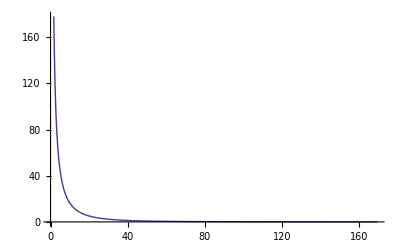

```mathematica
Print["We plot this integrand over range of Figure.  In the figure the function is multiplied by k^(3/2).  Since the integrand seems divergent as k-->0 we incorporate this k^(3/2)  factor, really kkeq^(3/2), into the integrand."]
ketamax=10 SubStar[η] keta0max/Subscript[η, 0]
Plot[integrand824Hu[keta0,ketamax,kkeq=keta0/(Subscript[η, 0] keq)],{keta0,0.01ketamax,ketamax},
PlotRange->{{0,ketamax},All},
AxesLabel->{"kη max"}
]
```

```mathematica
Print["Limit integrand824Hu as  k->0 : ",
Limit[
integrand824Hu[keta0,ketastar=SubStar[η] keta0/Subscript[η, 0],kkeq=keta0/(Subscript[η, 0] keq)]
,keta0->0
],"
The series approximation near keta==0 to the integrand : ",
Series[integrand824Hu[keta0,ketastar=SubStar[η] keta0/Subscript[η, 0],kkeq=keta0/(Subscript[η, 0] keq)],{keta0,0,2}]//Normal//Simplify
]
Subscript[η, 0]
```

Limit integrand824Hu as  k->0 : -∞
The series approximation near keta==0 to the integrand : ⅇ^(-3.74823 keta0^1.6) (-0.00698011 keta0-0.22871)+ⅇ^(-3.30525 keta0^1.6) (-0.0069729 keta0-0.228473)-195.524/keta0+0.457183

4.84617×10^18

```mathematica
ni=200;
keta0limit={0,keta0max};
list=Table[{
keta0X=i keta0limit[[2]]/ni,
ketastar=SubStar[η] keta0X/Subscript[η, 0],
kkeq=keta0X/(Subscript[η, 0] keq),
NIntegrate[
integrand824Hu[keta0,ketastar,kkeq],{keta0,0.00001 ketastar,ketastar},
Method->{"LocalAdaptive"}]
},{i,1,ni}];
list;
```

#### This plot of Eqn.8.24 has more oscillations than the one presented in the book. => there must be some differences in the computation of k r_s argument for Cos, Sin terms.

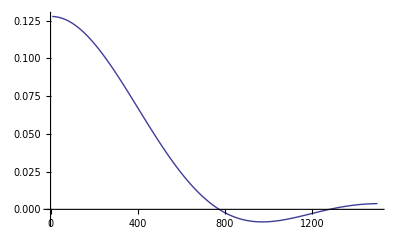

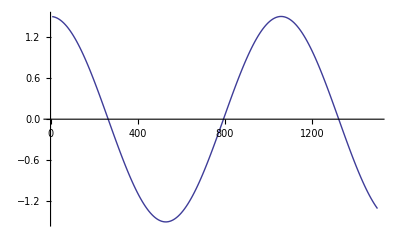

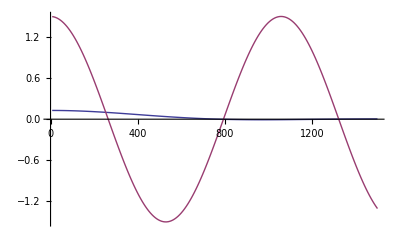

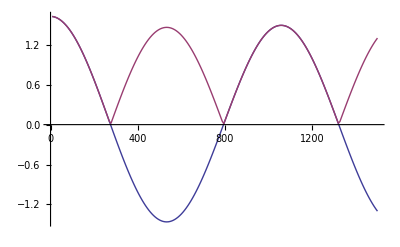

```mathematica
list0=Table[{list[[i,1]],  list[[i,4]]},{i,1,ni}];
ListLinePlot[Tooltip[list0,"∫"],PlotRange->{{0,keta0max},Full},AxesLabel->{"kη_0"}]

list1=Table[{
keta0X=i keta0max/ni,
ketastar=SubStar[η] keta0X/Subscript[η, 0];
kkeq=keta0X/(Subscript[η, 0] keq);(Φ0+Θ0) Cos[ krs[kkeq,ketastar]]/.subTheta0
},{i,1,ni}];
ListLinePlot[Tooltip[list1,"Φ_0Cos"],PlotRange->{{0,keta0max},Full},AxesLabel->{"kη_0"}]

list2=Table[{list[[i,1]], list0[[i,2]]+list1[[i,2]]},{i,1,Length[list]}];
list3=Table[{list[[i,1]],Abs[list2[[i,2]]]},{i,1,Length[list]}];
ListLinePlot[{Tooltip[list0,"∫"],Tooltip[list1,"Φ_0Cos"]},PlotRange->{{0,keta0max},Full},AxesLabel->{"kη_0"}]
ListLinePlot[{Tooltip[list2,"∫+Φ_0Cos"],Tooltip[list3,"|∫+Φ_0Cos|"]},PlotRange->{{0,keta0max},Full},AxesLabel->{"kη_0"}]
```

#### Investigate krs[kkeq,keta]; Compare with k r_s[kkeq,keta0] => krs[kkeq,keta] looks OK. So what is wrong with the period of the above plot.

```mathematica
xketa0;
ni=20
list1=Table[{
xketa0=i keta0max/ni,
xkkeq=xketa0/(Subscript[η, 0] Subscript[k, eq])//NumericalValues,
krs[xkkeq,xketa0],
xkkeq keq Subscript[r, s][ xketa0/xkkeq/Subscript[k, eq]]//NumericalValues,
(xkkeq keq Subscript[r, s][ (100 SubStar[η] xketa0/Subscript[η, 0]/xkkeq/Subscript[k, eq])]-
xkkeq keq Subscript[r, s][ xketa0/xkkeq/Subscript[k, eq]])//NumericalValues,
( krs[xkkeq, 100 SubStar[η] xketa0/Subscript[η, 0]]-krs[xkkeq,xketa0])
},
{i,1,ni}]
```

20

(75 | 1.12057 | 6.61559 | 6.61559 | 0.249457 | 0.249457
150 | 2.24113 | 13.2312 | 13.2312 | 0.498913 | 0.498913
225 | 3.3617 | 19.8468 | 19.8468 | 0.74837 | 0.74837
300 | 4.48227 | 26.4623 | 26.4623 | 0.997826 | 0.997826
375 | 5.60283 | 33.0779 | 33.0779 | 1.24728 | 1.24728
450 | 6.7234 | 39.6935 | 39.6935 | 1.49674 | 1.49674
525 | 7.84396 | 46.3091 | 46.3091 | 1.7462 | 1.7462
600 | 8.96453 | 52.9247 | 52.9247 | 1.99565 | 1.99565
675 | 10.0851 | 59.5403 | 59.5403 | 2.24511 | 2.24511
750 | 11.2057 | 66.1559 | 66.1559 | 2.49457 | 2.49457
825 | 12.3262 | 72.7714 | 72.7714 | 2.74402 | 2.74402
900 | 13.4468 | 79.387 | 79.387 | 2.99348 | 2.99348
975 | 14.5674 | 86.0026 | 86.0026 | 3.24294 | 3.24294
1050 | 15.6879 | 92.6182 | 92.6182 | 3.49239 | 3.49239
1125 | 16.8085 | 99.2338 | 99.2338 | 3.74185 | 3.74185
1200 | 17.9291 | 105.849 | 105.849 | 3.99131 | 3.99131
1275 | 19.0496 | 112.465 | 112.465 | 4.24076 | 4.24076
1350 | 20.1702 | 119.081 | 119.081 | 4.49022 | 4.49022
1425 | 21.2908 | 125.696 | 125.696 | 4.73968 | 4.73968
1500 | 22.4113 | 132.312 | 132.312 | 4.98913 | 4.98913)

#### How do these solutions compare with Hu.Sugiyama.Fig.1

```mathematica
Begin["Fig1`"];
Print["k value (1/sec) for Fig.1 : ",
keval=.065sec2Mpc//NumericalValues,"
'a' limits for Fig.1 : ",alimits={10^-6,.001},"
=> y limits : ",ylimits=alimits/Subscript[a, eq]//NumericalValues,"
=> η limits : ",etalimits=Subscript[η, y][ylimits]//NumericalValues,"
=>keta limits : ",ketalimits=etalimits keval
]
kkeq=keval/ keq
ni=300;
list=Table[{
ketaX=i  ketalimits[[2]]/ni;
etaX=ketaX/keval;
yX=y[etaX]//NumericalValues,
Reta=Subscript[R, η][etaX]//NumericalValues;
(1+Reta);
NIntegrate[
integrand824Hu[ keta, ketaX,kkeq  ],{keta,0.00000001, ketaX},
Method->{"LocalAdaptive"}],
krs[kkeq,ketaX];
(-Φ0+Θ0/.subTheta0)Cos[krs[kkeq,ketaX]],
Ψy[kkeq,yX]
},{i,1,ni}];
list;
End[];
```

k value (1/sec) for Fig.1 : 6.31968×10^-16
'a' limits for Fig.1 : {1/1000000,0.001}
=> y limits : {0.000607287,0.607287}
=> η limits : {6.21754×10^13,5.48418×10^16}
=>keta limits : {0.0392928,34.6583}

45.7583

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`keta near TraditionalForm`{keta} = TraditionalForm`{1.0000000000000388886050197557738260239268465246618061022172911001×10^-8}. NIntegrate obtained TraditionalForm`-7.63025×10^-11 and TraditionalForm`6.3750447575244474`*^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`keta near TraditionalForm`{keta} = TraditionalForm`{1.0000000000000551287074982324365249284914987524282993313037065282×10^-8}. NIntegrate obtained TraditionalForm`-4.35993×10^-10 and TraditionalForm`3.642694035146332`*^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`keta near TraditionalForm`{keta} = TraditionalForm`{1.36564×10^-6}. NIntegrate obtained TraditionalForm`-2.40223×10^-15 and TraditionalForm`4.7306182097397443`*^-17 for the integral and error estimates.

General::stop: Further output of TraditionalForm`NIntegrate :: "ncvb" will be suppressed during this calculation.

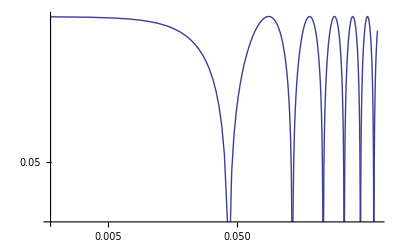

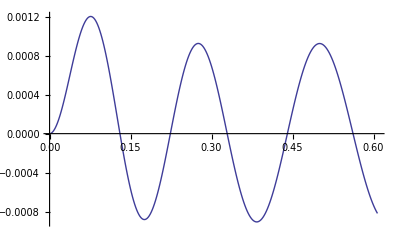

```mathematica
list;
list1=Table[{list[[i,1]],Abs[list[[i,2]]+list[[i,3]]-list[[i,4]]]},{i,1,Length[list]}];
ListLogLogPlot[list1,Joined->True,PlotRange->Automatic]

list1=Table[{list[[i,1]],list[[i,2]]},{i,1,Length[list]}];
ListPlot[list1,Joined->True,PlotRange->Full]
```

#### Are the R factors significant for Fig.1 of Hu?

```mathematica
Clear[kkeq]
Subscript[R, η][eta]/.eta->keta/(kkeq Subscript[k, eq])//Expand
```

(0.09375 keta^2)/kkeq^2+(0.53033 keta)/kkeq

#### Look for analytic form of integral

```mathematica
integrand824Hu[ketaP_,keta_,kkeq_]:=1/(√3)(Φ[kkeq,ketaP]-Ψ[kkeq,ketaP]) Sin[( Dkrs[kkeq,keta,ketaP])]


Φ[kkeq_,η_]:=Φy[kkeq,y[η]]
Ψ[kkeq_,η_]:=Ψy[kkeq,y[η]]
Φy[kkeq_,y_]:=Φbar[kkeq,y]((1-T[kkeq])ⅇ^(-.11(y kkeq)^1.6)+T[kkeq])
Ψy[kkeq_,y_]:=Ψbar[kkeq,y]((1-T[kkeq])ⅇ^(-.097( y kkeq)^1.6)+T[kkeq])
T[kkeq_]:=Log[1+.171 kkeq]/(.171 kkeq)(1+.284 kkeq+(1.18 kkeq  )^2+(.399 kkeq )^3+(.49 kkeq )^4)^(-.25)
Φbar[kkeq_,y_]:=3/4(1/kkeq )^2(y+1)/y^2 Subscript[Δ, T][y]
Ψbar[kkeq_,y_]:=-3/4(1/kkeq )^2(y+1)/y^2(Subscript[Δ, T][y]+.65 N2[y]/(1+y))
N2[y_]:=-0.1(20 y +19)/(3 y +4)y^2/(y+1)Φls[y]-8/3 y/(3 y +4)+8/9 Log[3 y/4+1]
Subscript[Δ, T][y_]:=(1.16-(.48 y)/(y+1))Φls[y] y^2/(y+1)
Φls0[y_]:=Φ0/10 1/y^3(16 √(1+y)+9 y^3+2 y^2-8 y-16)
PhiSeries[y_]:=(Series[Φls0[yyy],{yyy,0,3}]//Normal)/.yyy->y;
Φls[y_]:=Φls0[y]
(**)

Clear[Φls,T,y]

integrand824Hu[ ketaP, keta,kkeq  ]//Simplify;
integd=%/.y[ketaP]->Y;

y[eta_]:=y/.subyeta/.xeta->eta//Simplify;
y[ketaXX/(kkeqXX Subscript[k, eq])]==yXX;
subketay=Solve[%,ketaXX][[2]]//FullSimplify;
ketay[y_,kkeq_]:=ketaXX/.subketay/.yXX->y/.kkeqXX->kkeq;

Dkrs[kkeq,keta,ketaP]/.keta->ketay[y,kkeq]/.ketaP->ketay[yP,kkeq];
Print[" integrand824Hu[ ketaP, keta,kkeq] in terms of yP, y, and kkeq : ",
integd1=integd/.keta->ketay[y,kkeq]/.ketaP->ketay[yP,kkeq]/.Y->y//PowerExpand//Simplify
]
Integrate[integd1,y]
```

integrand824Hu[ ketaP, keta,kkeq] in terms of yP, y, and kkeq : 1/(4 kkeq^2)√3 sin(4/3 √2 kkeq (sinh^-1(√3 √(y+1))-sinh^-1(√3 √(yP+1)))) ((1.16-(0.48 y)/(y+1)) (T(kkeq)-ⅇ^(-0.11 kkeq^1.6 y^1.6) (T(kkeq)-1)) Φls(y)+1/(y^2 (y+1.) (3. y+4.))ⅇ^(-0.097 kkeq^1.6 y^1.6) ((-1.+ⅇ^(0.097 kkeq^1.6 y^1.6)) T(kkeq)+1.) ((2.04 y^2+4.9 y+3.405) Φls(y) y^2+(1.73333 log(1. y+1.33333) y-2.23198 y-1.73333) y+(4.04444 y+2.31111) log(0.75 y+1.)))

1/(4 kkeq^2)√3 ∫sin(4/3 √2 kkeq (sinh^-1(√3 √(y+1))-sinh^-1(√3 √(yP+1)))) ((1.16-(0.48 y)/(y+1)) (T(kkeq)-ⅇ^(-0.11 kkeq^1.6 y^1.6) (T(kkeq)-1)) Φls(y)+1/(y^2 (y+1.) (3. y+4.))ⅇ^(-0.097 kkeq^1.6 y^1.6) ((-1.+ⅇ^(0.097 kkeq^1.6 y^1.6)) T(kkeq)+1.) ((2.04 y^2+4.9 y+3.405) Φls(y) y^2+(1.73333 log(1. y+1.33333) y-2.23198 y-1.73333) y+(4.04444 y+2.31111) log(0.75 y+1.)))ⅆy